```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
Clear[Δ]
Clear[ω]
dispersion=Solve[0==Det[{{-ω^2+I*η*ω+2*κ+1/(1+Δ),2*κ*(1-Δ)/(1+Δ)*Cos[q/2]},{2*κ*(1+Δ)/(1-Δ)*Cos[q/2],-ω^2+I*η*ω+2*κ+1/(1-Δ)}}],ω];
spring[p0_,p1_,divs_,height_]:=Module[{L,xhat,yhat},L=Norm[p1-p0]; xhat=(p1-p0)/L; yhat={xhat[[2]],-xhat[[1]]};Join[{p0,p0+L/divs*xhat},Table[p0+i*L/divs*xhat+height*yhat*(-1)^i,{i,2,divs-2}],{p1-L/divs*xhat,p1}]];
ωmin=3.3;
ωmax=3.7;
Amin=0.0;
Amax=0.08;
Npoints=100;
M=32;
M2=3;
κ=1;
η=0.1;
cf[x_]:=Lighter[Blend[{Yellow,Red},(x-0.45)/(0.7-0.45)]]
cf[x_]:=Lighter[Red]

M2=5;
A1[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2))*KroneckerDelta[i,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A2[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*2*n+I*ω*η))*KroneckerDelta[i,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A3[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*n^2+I*ω*η*n+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(KroneckerDelta[i,1]*KroneckerDelta[j,2]+Exp[I*q]*KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(Exp[-I*q]*KroneckerDelta[i,1]*KroneckerDelta[j,2]+KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m]+a*ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A[a_,ω_,Δ_,q_]:=ArrayFlatten[{{A3[a,ω,Δ,q],A2[a,ω,Δ,q]},{ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}],IdentityMatrix[2*(2*M2+1)]}}]
B[a_,ω_,Δ_,q_]:=ArrayFlatten[{{ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}],-A1[a,ω,Δ,q]},{IdentityMatrix[2*(2*M2+1)],ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}]}}]
A4[ω_,Δ_,q_,ϵ_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*(ϵ+n)^2+I*ω*η*(ϵ+n)+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(KroneckerDelta[i,1]*KroneckerDelta[j,2]+Exp[I*q]*KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(Exp[-I*q]*KroneckerDelta[i,1]*KroneckerDelta[j,2]+KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
B4[ω_]:=ArrayFlatten[Table[-ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
```

/home/zack/oscillators/anharmonic

## Direct simulations

```mathematica
filebase="data/noisy";
{M,freq,amp,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
Dimensions[dat]
norms=Total/@Abs[dat[[All,1;;32]]]^2/M;
max=Max[Mod[dat[[-500;;-1,1;;32]]+Pi,2*Pi]-Pi]
min=Min[Mod[dat[[-500;;-1,1;;32]]+Pi,2*Pi]-Pi]
cf[x_]:=ColorData["TemperatureMap"][(x-min)/(max-min)];
Grid[{{ListPlot[Log[norms],Joined->True,ImageSize->300,ImageSize->300],ListPlot[{dat[[-500;;-1,1]],Cos[2*Pi*dt*Range[500]]},PlotRange->All,Joined->True,ImageSize->300],ListDensityPlot[Mod[dat[[1;;-1;;2*Round[1/dt],1;;M]]+Pi,2*Pi]-Pi,ImageSize->500,AspectRatio->1,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False,PlotRange->All,InterpolationOrder->0]}}]
```

{32,3.4,0.05,0.05,0.1,0.05,0.5,5000.,1,5}

{100000,64}

1.14119

-0.708902

-Graphics-

{32,3.4,0.05,0.05,0.1,0.,0.5,5000.,1,1}

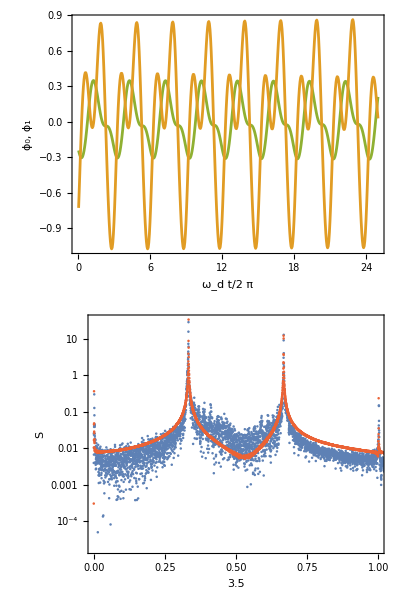

series.pdf

```mathematica
filebase="data/anharmonic";
{M,freq,amp,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat1=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
filebase="data/noisy";
dat2=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];

Clear[t];
p1=ListPlot[{Transpose[{dt*Range[500],dat1[[-500;;-1,1]]}],Transpose[{dt*Range[500],dat1[[-500;;-1,2]]}]},PlotRange->All,Joined->True,AspectRatio->1/3,Axes->False,Frame->True,PlotStyle->{Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]},FrameLabel->{DisplayForm[RowBox[{HoldForm[Subscript[ω,d]*t],"/",2π}]],DisplayForm[RowBox[{Style[Subscript[ϕ,0],ColorData[97,"ColorList"][[2]]],", ",Style[Subscript[ϕ,1],ColorData[97,"ColorList"][[3]]]}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],ImagePadding->{{75,25},{75,25}}, ImageSize->400];

n0=1000;
n2=Position[Differences[Sign[Differences[Total[Abs[#-dat1[[n0/dt]]]^2]&/@dat1]]],2][[-1,1]];
power1=Abs[Fourier[dat1[[n0/dt;;n2,1]]]];
freqs1=Range[Length[dat1[[n0/dt;;n2,1]]]]/(Length[dat1[[n0/dt+1;;n2,1]]]*dt);
power2=Abs[Fourier[dat2[[n0/dt;;n2,1]]]];
freqs2=Range[Length[dat2[[n0/dt;;n2,1]]]]/(Length[dat2[[n0/dt+1;;n2,1]]]*dt);
p2=ListLogPlot[{Transpose[{freqs2,power2}],Transpose[{freqs1,power1}]},PlotRange->{{0,1},All},PlotStyle->{Directive[PointSize[0.0045],ColorData[97,"ColorList"][[1]]],Directive[PointSize[0.0045],ColorData[97,"ColorList"][[4]]]},Axes->False,Frame->True,FrameLabel->{ω,S},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{75,25},{75,25}}, ImageSize->400];
p=Grid[{{p1},{p2}}]
Export["series.pdf",p]
```

{1.79719,Null}

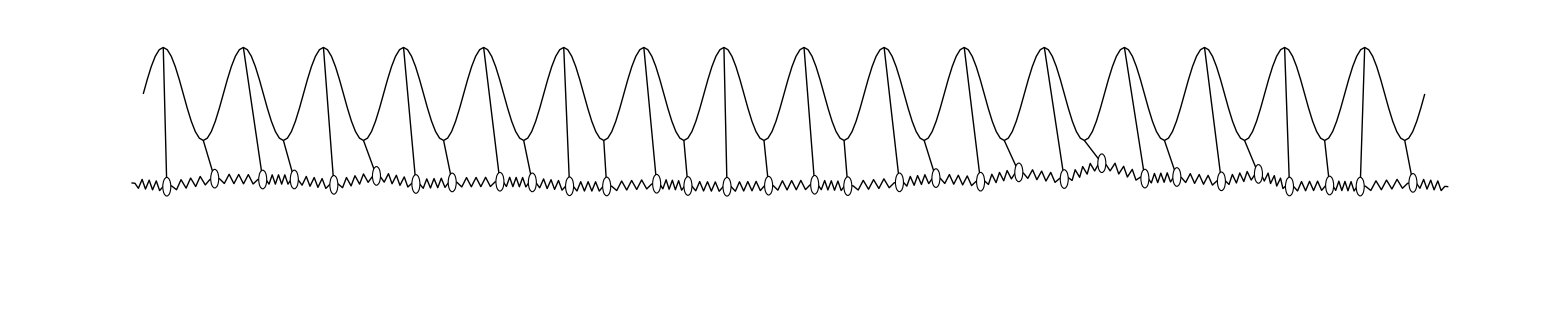

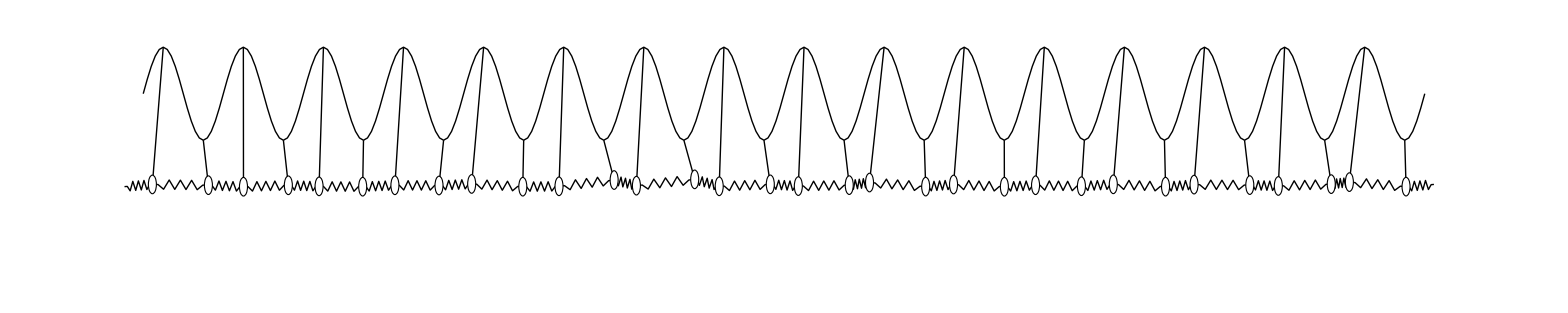

```mathematica
dx=1;
Monitor[AbsoluteTiming[plots=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
thetas=dat[[n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/freq;
z0={0,amp*Cos[freq*t]};
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],White,Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Black,Line[Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}]]},ImageSize->2000,PlotRange->{dx*{1/2,M+1/2},{-1,1.75}}];
p0,{n,Max[1,Length[dat]-499],Length[dat]}];],N[(n-Max[1,Length[dat]-499])/(1+Length[dat]-Max[1,Length[dat]-499])]]
plots[[1]]
plots[[-1]]
```

```mathematica
If[!DirectoryQ[filebase<>"animation"],CreateDirectory[filebase<>"animation"]]
ParallelDo[Export[filebase<>"animation/"<>IntegerString[n,10,4]<>".png",plots[[n]]],{n,1,Length[plots]}]
```

## Floquet exponents

{-5.66688+0.0142857 ⅈ,5.66688+0.0142857 ⅈ,5.31699+0.0142857 ⅈ,-5.31699+0.0142857 ⅈ,-4.67197+0.0290099 ⅈ,4.67197+0.0290099 ⅈ,-4.67197-0.000438423 ⅈ,4.67197-0.000438423 ⅈ,4.32883+0.0289812 ⅈ,-4.32883+0.0289812 ⅈ,4.32883-0.000409731 ⅈ,-4.32883-0.000409731 ⅈ,3.67145+0.0291685 ⅈ,-3.67145+0.0291685 ⅈ,-3.67145-0.000597025 ⅈ,3.67145-0.000597025 ⅈ,3.32855+0.0291685 ⅈ,-3.32855+0.0291685 ⅈ,-3.32855-0.000597025 ⅈ,3.32855-0.000597025 ⅈ,-2.67145+0.0291685 ⅈ,2.67145+0.0291685 ⅈ,-2.67145-0.000597051 ⅈ,2.67145-0.000597051 ⅈ,-2.32855+0.0291685 ⅈ,2.32855+0.0291685 ⅈ,2.32855-0.000597051 ⅈ,-2.32855-0.000597051 ⅈ,1.67145+0.0291685 ⅈ,-1.67145+0.0291685 ⅈ,-1.67145-0.000597051 ⅈ,1.67145-0.000597051 ⅈ,1.32855+0.0291685 ⅈ,-1.32855+0.0291685 ⅈ,-1.32855-0.000597051 ⅈ,1.32855-0.000597051 ⅈ,0.671448+0.0291685 ⅈ,-0.671448+0.0291685 ⅈ,-0.671448-0.000597051 ⅈ,0.671448-0.000597051 ⅈ,0.328552+0.0291685 ⅈ,-0.328552+0.0291685 ⅈ,0.328552-0.000597051 ⅈ,-0.328552-0.000597051 ⅈ}

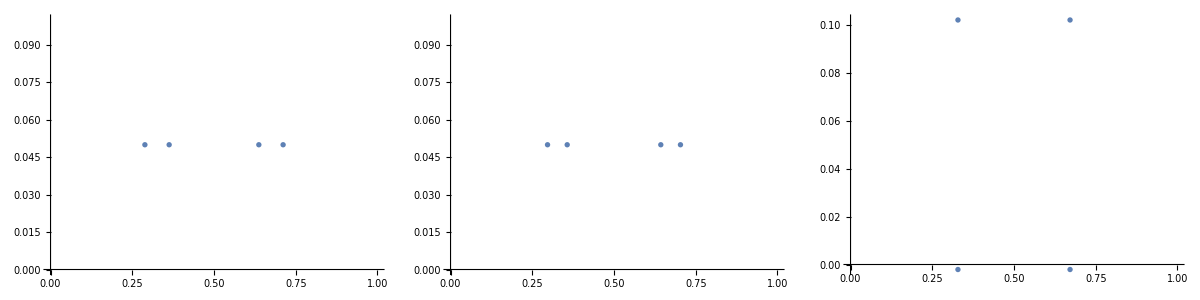

{3.5329×10^-15-9.01058×10^-16 ⅈ,6.48335×10^-13+2.36343×10^-13 ⅈ,3.74814×10^-13+4.14833×10^-14 ⅈ,5.42851×10^-14-2.51595×10^-13 ⅈ,2.69279×10^-13-1.10012×10^-13 ⅈ,-3.14599×10^-13-3.39702×10^-13 ⅈ,-1.09105×10^-14+1.69257×10^-14 ⅈ,7.56719×10^-15-6.48742×10^-14 ⅈ,6.42542×10^-14-7.79932×10^-14 ⅈ,7.97314×10^-14-1.09187×10^-13 ⅈ,9.43343×10^-15-2.56739×10^-16 ⅈ,2.19425×10^-14-4.48183×10^-14 ⅈ,3.4639×10^-14-2.4647×10^-14 ⅈ,2.9754×10^-14-1.03473×10^-13 ⅈ,4.996×10^-15+1.01447×10^-14 ⅈ,-2.74086×10^-16-1.34441×10^-14 ⅈ,1.0133×10^-15+4.07725×10^-15 ⅈ,-1.05318×10^-15-4.28206×10^-16 ⅈ,3.44553×10^-16+1.20761×10^-15 ⅈ,-6.08239×10^-16-5.48512×10^-16 ⅈ,1.15958×10^-15+6.23276×10^-16 ⅈ,1.79762×10^-17+1.64895×10^-15 ⅈ}

```mathematica
ω=3.5;
Δ=0.5;
q=0;
a=0.05;
{evals,evecs}=Eigensystem[{A[a,ω,Δ,q],B[a,ω,Δ,q]}];
evals
Grid[{{ListPlot[{Re[#],ω*Im[#]}&/@Eigenvalues[{A[a,ω,0,q],B[a,ω,0,q]}],PlotRange->{{0,1},All},ImageSize->300],ListPlot[{Re[#],ω*Im[#]}&/@Eigenvalues[{A[a,ω,Δ/2,q],B[a,ω,Δ/2,q]}],PlotRange->{{0,1},All},ImageSize->300],ListPlot[{Re[#],ω*Im[#]}&/@Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}],PlotRange->{{0,1},All},ImageSize->300]}}]
val=evals[[-1]];
vec=evecs[[-1,1;;2*(2*M2+1)]];
val^2*A1[a,ω,Δ,q].vec+val*A2[a,ω,Δ,q].vec+A3[a,ω,Δ,q].vec
```

### Individual parameters

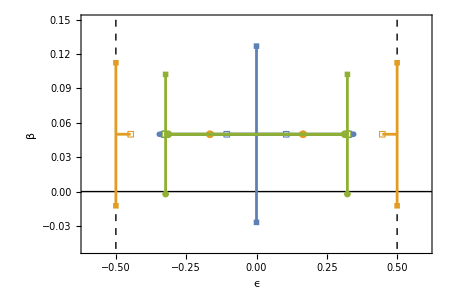

```mathematica
Clear[ω]
ωd=1.0;
amin=0.01;
amax=0.8;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5];
p1=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.04]],PlotMarkers->{Graphics[{Circle[{0,0},0.02]},PlotRange->{-1,1}],Graphics[{EdgeForm[ColorData[97,"ColorList"][[1]]], White, Rectangle[{-0.02,-0.02},{0.02,0.02}]},PlotRange->{-1,1}],Graphics[{Disk[{0,0},0.02]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.04,-0.04},{0.04,0.04}]},PlotRange->{-1,1}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]]},Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}}]];
ωd=2.0;
amin=0.01;
amax=0.12;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p2=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[5;;6]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],PointSize[0.04]],PlotMarkers->{Graphics[{EdgeForm[ColorData[97,"ColorList"][[2]]],White,Rectangle[{-0.02,-0.02},{0.02,0.02}]},PlotRange->{-1,1}],Graphics[{Circle[{0,0},0.02]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.04,-0.04},{0.04,0.04}]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.04,-0.04},{0.04,0.04}]},PlotRange->{-1,1}],Graphics[{EdgeForm[ColorData[97,"ColorList"][[2]]],Disk[{0,0},0.02]},PlotRange->{-1,1}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals2[[{2,3}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,4}]],{{Re[#],ωd*Im[#]},{-0.5,ωd*Im[#]}}&@evals1[[1]],{{Re[#],ωd*Im[#]},{0.5,ωd*Im[#]}}&@evals1[[2]]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]];
ωd=3.4;
amin=0.0;
amax=0.05;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p3=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],PointSize[0.04]],PlotMarkers->{Graphics[{EdgeForm[ColorData[97,"ColorList"][[3]]],White,Rectangle[{-0.02,-0.02},{0.02,0.02}]},PlotRange->{-1,1}],Graphics[{Circle[{0,0},0.02]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.04,-0.04},{0.04,0.04}]},PlotRange->{-1,1}],Graphics[{EdgeForm[ColorData[97,"ColorList"][[3]]],Disk[{0,0},0.04]},PlotRange->{-1,1}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals2[[{1,3}]],{Re[#],ωd*Im[#]}&/@evals2[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals1[[{1,4}]],{Re[#],ωd*Im[#]}&/@evals1[[{2,3}]]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]];
p1=Show[p1,p2,p3,AspectRatio->2/3,ImageSize->450,ImagePadding->{{75,25},{75,25}}]
```

```mathematica
ωd=3.4;
AbsoluteTiming[Monitor[test1=Table[Eigenvalues[{A4[ωd,0,0,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
AbsoluteTiming[Monitor[test2=Table[Eigenvalues[{A4[ωd,Δ,0,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
AbsoluteTiming[Monitor[test3=Table[Eigenvalues[{A4[ωd,0,Pi,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
AbsoluteTiming[Monitor[test4=Table[Eigenvalues[{A4[ωd,Δ,Pi,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
```

{4.44604,Null}

{4.83498,Null}

{5.63013,Null}

{6.25323,Null}

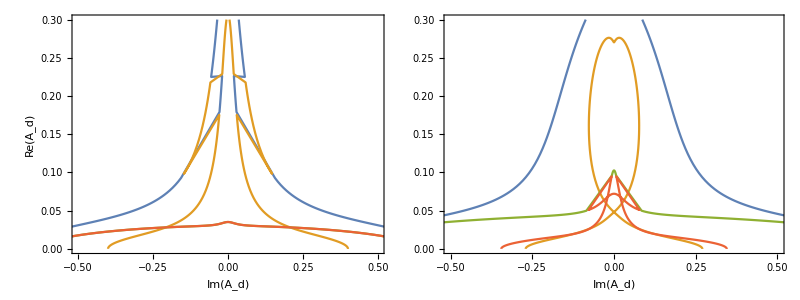
-Graphics-
-Graphics-

fig3.pdf

```mathematica
p2=Grid[{{ListPlot[Join[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test1[[2;;-1,-4;;-1]])],Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test3[[2;;-1,-4;;-1]])]],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->250,PlotRange->{{-0.5,0.5},{0,0.3}},ImagePadding->{{50,10},{50,10}}],ListPlot[Join[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test2[[2;;-1,-4;;-1]])],Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test4[[2;;-1,-4;;-1]])]],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],None},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->250,PlotRange->{{-0.5,0.5},{0,0.3}},ImagePadding->{{50,10},{50,10}}]}}];
p=Grid[{{p1},{p2}}]
Export["fig3.pdf",p]
```

```mathematica
cf[x_]:=Blend[{Lighter[Red],Lighter[Yellow]},x];

p0=Legended[ListDensityPlot[Join[#[[{1,2,4}]]&/@Cases[test3,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[test3,u_/;u[[3]]≥0]],PlotRange->{-0.01,0.51},ColorFunctionScaling->True,ColorFunction->cf,InterpolationOrder->1,ImageSize->300,FrameLabel->{ω,Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]]],Placed[MatrixPlot[Table[cf[-Pi+2*Pi*(i-1)/100],{i,1,100},{j,1,10}],PlotRangePadding->None,FrameTicks->{{None,{{1,PaddedForm[0.0,{3,3}]},{25,PaddedForm[0.125,{3,3}]},{50,PaddedForm[0.25,{3,3}]},{75,PaddedForm[0.325,{3,3}]},{100,PaddedForm[0.5,{3,3}]}}},{None,None}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->15,ImageSize->{Automatic,200},PlotLabel->ϵ,PlotRange->{{1,100},{1,10}},DataReversed->{True,False}],Right]]
```

-Graphics-

### Large sweep

```mathematica
M=100;
ωmin=0.5;
ωmax=5.0;
amin=0;
amax=1.0;
num=100;AbsoluteTiming[Monitor[vals1=N[{#[[1]],#[[2]],2*Im[#[[3,2]]],Re[#[[3,2]]],#[[3,1]]}]&/@Flatten[Table[{ω,a,First[MinimalBy[Flatten[ParallelTable[Cases[Transpose[{ConstantArray[q,4*(2*M2+1)],Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}]}],u_/;Re[u[[2]]]>-0.1&&Re[u[[2]]]≤0.6],{q,0,Pi,4*Pi/M}],1],Im[#[[2]]]&]]},{ω,ωmin,ωmax,(ωmax-ωmin)/num},{a,amin,amax,(amax-amin)/num}],1];,{(a-amin)/(amax-amin),(ω-ωmin)/(ωmax-ωmin)}]]
ωmin=3.0;
ωmax=4.0;
amin=0;
amax=0.1;
num=100;
AbsoluteTiming[Monitor[vals2=N[{#[[1]],#[[2]],2*Im[#[[3,2]]],Re[#[[3,2]]],#[[3,1]]}]&/@Flatten[Table[{ω,a,First[MinimalBy[Flatten[ParallelTable[Cases[Transpose[{ConstantArray[q,4*(2*M2+1)],Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}]}],u_/;Re[u[[2]]]>-0.1&&Re[u[[2]]]≤0.6],{q,0,Pi,4*Pi/M}],1],Im[#[[2]]]&]]},{ω,ωmin,ωmax,(ωmax-ωmin)/num},{a,amin,amax,(amax-amin)/num}],1];,{(a-amin)/(amax-amin),(ω-ωmin)/(ωmax-ωmin)}]]
```

{576.408,Null}

{564.446,Null}

```mathematica
Export["data/vals1.dat",vals1]
Export["data/vals2.dat",vals2]
```

data/vals1.dat

data/vals2.dat

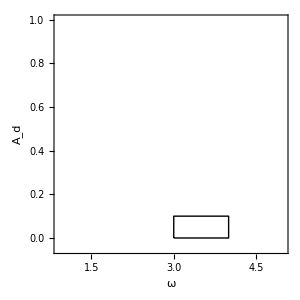
-Graphics- | -Graphics-

boundary.pdf

```mathematica
vals1=Import["data/vals1.dat"];
vals2=Import["data/vals2.dat"];
cf[x_]:=ColorData["Rainbow"][(x)/(Pi)];
p1=Legended[rasterizeBackground[ListDensityPlot[Join[#[[{1,2,5}]]&/@Cases[vals1,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals1,u_/;u[[3]]≥0]],PlotRange->{{0.9,5},{-0.05,1},{0,2*Pi}},InterpolationOrder->1,ImageSize->300,FrameLabel->{"ω",Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False,Epilog->{Line[{{3,0},{4,0},{4,0.1},{3,0.1},{3,0}}]}]],Placed[MatrixPlot[Table[cf[Pi*(i-1)/100],{i,1,100},{j,1,10}],PlotRangePadding->None,FrameTicks->{{None,{{1,0},{25,DisplayForm[RowBox[{π,"/",2}]]},{50,π},{75,DisplayForm[RowBox[{3π,"/",2}]]},{100,2π}}},{None,None}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->10,ImageSize->{Automatic,150},PlotLabel->k,PlotRange->{{1,100},{1,10}},DataReversed->{True,False}],Right]];
cf[x_]:=Blend[{Lighter[Red],Lighter[Yellow]},(x-min)/(max-min)];
p2=Legended[rasterizeBackground[Show[ListDensityPlot[Join[{#[[1]],#[[2]],1-#[[4]]}&/@Cases[vals2,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals2,u_/;u[[3]]≥0]],PlotRange->{min-0.1,All},InterpolationOrder->1,ImageSize->300,ColorFunction->cf,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"ω",Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]]],ListPlot[{{3.4,0.05}},PlotStyle->Directive[Black,PointSize[0.04]]]]],Placed[MatrixPlot[Table[cf[min+(max-min)*(i-1)/100],{i,1,100},{j,1,10}],PlotRangePadding->None,FrameTicks->{{None,{{1,PaddedForm[min,{3,3}]},{25,PaddedForm[min+0.25*(max-min),{3,3}]},{50,PaddedForm[min+0.5*(max-min),{3,3}]},{75,PaddedForm[min+0.75*(max-min),{3,3}]},{100,PaddedForm[max,{3,3}]}}},{None,None}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->10,ImageSize->{Automatic,150},PlotLabel->ϵ,PlotRange->{{1,100},{1,10}},DataReversed->{True,False}],Right]];
p=Grid[{{p1,p2}}]
Export["boundary.pdf",p]
```

### boundary loops

```mathematica
AbsoluteTiming[Monitor[test1=Table[Eigenvalues[{A4[ω,0,Pi/2,ϵ],B4[ω]}],{ϵ,0,1,0.01}];,ϵ]]
AbsoluteTiming[Monitor[test2=Table[Eigenvalues[{A4[ω,Δ,Pi/2,ϵ],B4[ω]}],{ϵ,0,1,0.01}];,ϵ]]
AbsoluteTiming[Monitor[test3=Table[Eigenvalues[{A4[ω,0,Pi,ϵ],B4[ω]}],{ϵ,0,1,0.01}];,ϵ]]
AbsoluteTiming[Monitor[test4=Table[Eigenvalues[{A4[ω,Δ,Pi,ϵ],B4[ω]}],{ϵ,0,1,0.01}];,ϵ]]
```

{1.07002,Null}

{1.17581,Null}

{1.05692,Null}

{1.10161,Null}

{5.46611,Null}

{5.96006,Null}

{5.28746,Null}

{7.05712,Null}

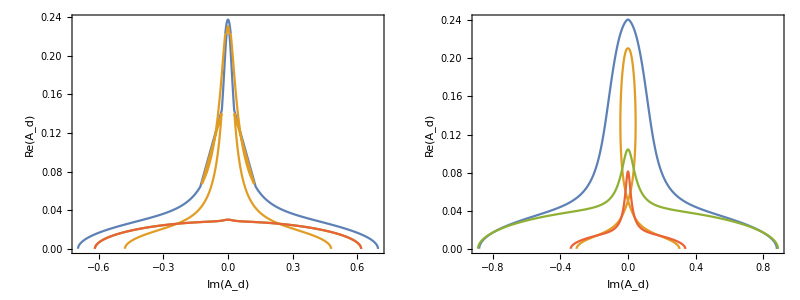

loop.pdf

```mathematica
A4[ω_,Δ_,q_,ϵ_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*(ϵ+n)^2+I*ω*η*(ϵ+n)+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(KroneckerDelta[i,1]*KroneckerDelta[j,2]+Exp[I*q]*KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(Exp[-I*q]*KroneckerDelta[i,1]*KroneckerDelta[j,2]+KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
B4[ω_]:=ArrayFlatten[Table[-ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
AbsoluteTiming[Monitor[test1=Table[Eigenvalues[{A4[ω,0,Pi/2,ϵ],B4[ω]}],{ϵ,0,1,0.002}];,ϵ]]
AbsoluteTiming[Monitor[test2=Table[Eigenvalues[{A4[ω,Δ,Pi/2,ϵ],B4[ω]}],{ϵ,0,1,0.002}];,ϵ]]
AbsoluteTiming[Monitor[test3=Table[Eigenvalues[{A4[ω,0,Pi,ϵ],B4[ω]}],{ϵ,0,1,0.002}];,ϵ]]
AbsoluteTiming[Monitor[test4=Table[Eigenvalues[{A4[ω,Δ,Pi,ϵ],B4[ω]}],{ϵ,0,1,0.002}];,ϵ]]
p=Grid[{{ListPlot[Join[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test1[[2;;-1,-4;;-1]])],Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test3[[2;;-1,-4;;-1]])]],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->350,PlotRange->All],ListPlot[Join[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test2[[2;;-1,-4;;-1]])],Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test4[[2;;-1,-4;;-1]])]],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->350,PlotRange->All]}}]
Export["loop.pdf",p]
```

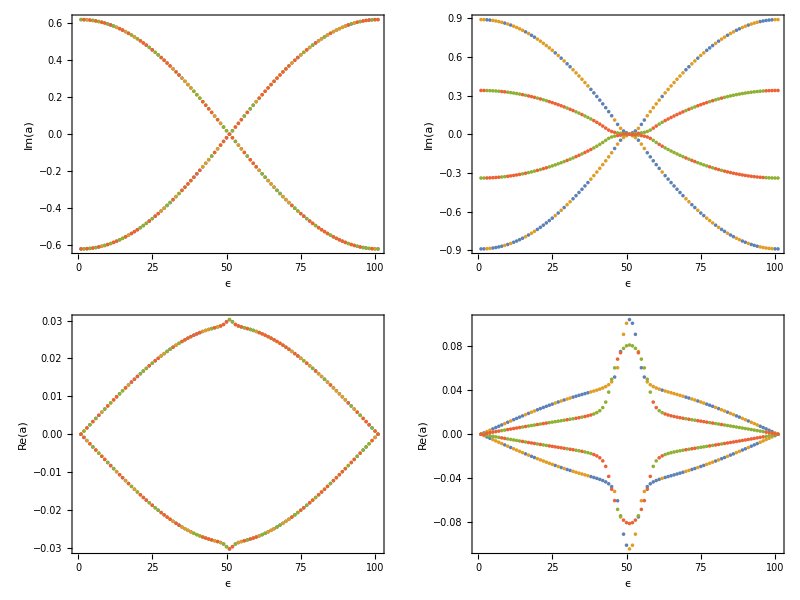
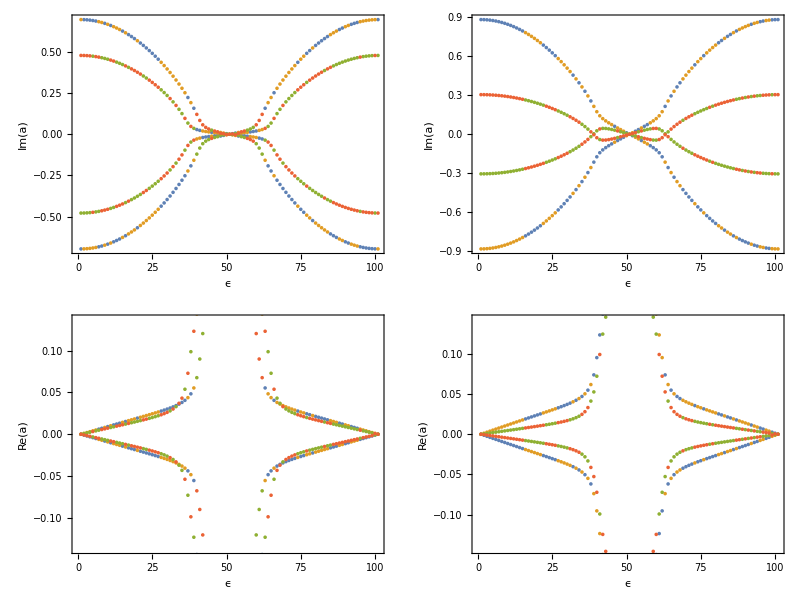
-Graphics- | -Graphics-

```mathematica
p1=ListPlot[Transpose[Im[test1][[All,-4;;-1]]],Joined->False,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{"ϵ",Im["a"]},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->350];
p2=ListPlot[Transpose[Im[test2][[All,-4;;-1]]],Joined->False,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{"ϵ",Im["a"]},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->350];
p3=ListPlot[Transpose[Re[test1][[All,-4;;-1]]],Joined->False,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{"ϵ",Re["a"]},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->350];
p4=ListPlot[Transpose[Re[test2][[All,-4;;-1]]],Joined->False,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{"ϵ",Re["a"]},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->350];
p5=ListPlot[Transpose[Im[test3][[All,-4;;-1]]],Joined->False,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{"ϵ",Im["a"]},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->350];
p6=ListPlot[Transpose[Im[test4][[All,-4;;-1]]],Joined->False,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{"ϵ",Im["a"]},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->350];
p7=ListPlot[Transpose[Re[test3][[All,-4;;-1]]],Joined->False,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{"ϵ",Re["a"]},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->350];
p8=ListPlot[Transpose[Re[test4][[All,-4;;-1]]],Joined->False,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{"ϵ",Re["a"]},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->350];
Grid[{{Grid[{{p5,p6},{p7,p8}}],Grid[{{p1,p2},{p3,p4}}]}}]
```

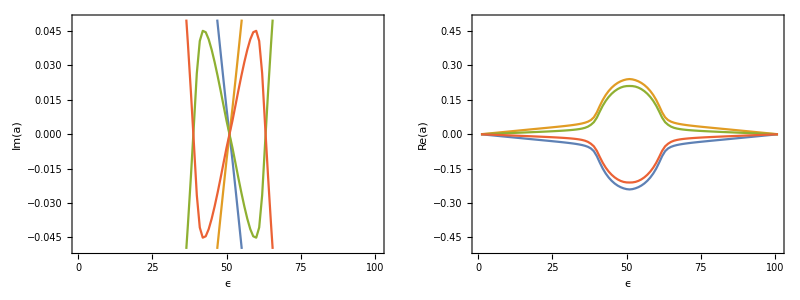

```mathematica
Monitor[test=Table[Eigenvalues[{A4[3.5,Δ,Pi/2,ϵ],B4[ω]}],{ϵ,0,1,0.01}];,ϵ]
n=4;
last=test[[1,-n;;-1]];sort1=Join[{test[[1,-n;;-1]]},Table[last=Table[First@MinimalBy[test[[i]],Abs[#-last[[j]]]&],{j,-n,-1}],{i,2,Length[test]}]];
p1=ListPlot[Transpose[Im[sort1]],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{"ϵ",Im["a"]},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->350,PlotRange->{-0.05,0.05}];
p3=ListPlot[Transpose[Re[sort1]],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{"ϵ",Re["a"]},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->350,PlotRange->{-0.5,0.5}];
Grid[{{p1,p3}}]
```